```mathematica
Phi[x_]:=1/2+1/2*Erf[x/Sqrt[2]]
```

## Logarithmic derivative

```mathematica
Series[2/(mu1*m1[t]+mu2*m2[t])*(mu1*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m1[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)]-lam*m1[t]) +mu2*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m2[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)] -lam*m2[t]))- 2/(m1[t]^2+m2[t]^2)*(m1[t]*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m1[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)]-lam*m1[t])+m2[t]*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m2[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)]-lam*m2[t])),{sigma,0,3}]
```

1/(2 (mu1 m1[t]+mu2 m2[t]) (m1[t]^2+m2[t]^2))(mu2^2 Erfc[-1/4 √π (mu1 m1[t]+mu2 m2[t])] Erfc[1/4 √π (mu1 m1[t]+mu2 m2[t])] m1[t]^2-2 mu1 mu2 Erfc[-1/4 √π (mu1 m1[t]+mu2 m2[t])] Erfc[1/4 √π (mu1 m1[t]+mu2 m2[t])] m1[t] m2[t]+mu1^2 Erfc[-1/4 √π (mu1 m1[t]+mu2 m2[t])] Erfc[1/4 √π (mu1 m1[t]+mu2 m2[t])] m2[t]^2)+1/(32 (mu1 m1[t]+mu2 m2[t]))ⅇ^(-1/8 π (mu1 m1[t]+mu2 m2[t])^2) (-mu2 m1[t]+mu1 m2[t])^2 (-4+ⅇ^(1/16 π (mu1 m1[t]+mu2 m2[t])^2) mu1 π Erf[1/4 √π (mu1 m1[t]+mu2 m2[t])] m1[t]+ⅇ^(1/16 π (mu1 m1[t]+mu2 m2[t])^2) mu2 π Erf[1/4 √π (mu1 m1[t]+mu2 m2[t])] m2[t]) sigma^2+O[sigma]^4

```mathematica
(-4+ⅇ^(1/16 π (mu1 m1[t]+mu2 m2[t])^2) mu1 π Erf[1/4 √π (mu1 m1[t]+mu2 m2[t])] m1[t]+ⅇ^(1/16 π (mu1 m1[t]+mu2 m2[t])^2) mu2 π Erf[1/4 √π (mu1 m1[t]+mu2 m2[t])] m2[t]) //FullSimplify
```

-4+ⅇ^(1/16 π (mu1 m1[t]+mu2 m2[t])^2) π Erf[1/4 √π (mu1 m1[t]+mu2 m2[t])] (mu1 m1[t]+mu2 m2[t])

```mathematica
Series[(2/(mu1*m1[t]+mu2*m2[t])*(mu1*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma1^2/Sqrt[2Pi](m1[t] Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma1^2/Sqrt[2Pi]*2m1[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]-lam*m1[t]) +mu2*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma2^2/Sqrt[2Pi](m2[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma2^2/Sqrt[2Pi]*2m2[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)] -lam*m2[t]))- 2/(m1[t]^2*sigma1^2+m2[t]^2*sigma2^2)*(m1[t]*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma1^2/Sqrt[2Pi](m1[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma1^2/Sqrt[2Pi]*2m1[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]-lam*m1[t])+m2[t]*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma2^2/Sqrt[2Pi](m2[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma2^2/Sqrt[2Pi]*2m2[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]-lam*m2[t]))//FullSimplify)/.{mu1->1,mu2->0,sigma1->1},{sigma2,0,3}]
```

(2 lam m2[t]^2)/m1[t]^2-(2 (lam m1[t]^2 m2[t]^2+lam m2[t]^4-2 m1[t] m2[t]^2 OwenT[(√π m1[t])/(√(8+π m1[t]^2)),2/(√(4+π m1[t]^2))]) sigma2^2)/m1[t]^4+O[sigma2]^4

## Anisotropic Logarithmic derivative

```mathematica
Series[(2/(mu1*m1[t]+mu2*m2[t])*(mu1*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma1^2/Sqrt[2Pi](m1[t] Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma1^2/Sqrt[2Pi]*2m1[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]-lam*m1[t]) +mu2*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma2^2/Sqrt[2Pi](m2[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma2^2/Sqrt[2Pi]*2m2[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)] -lam*m2[t]))- 2/(m1[t]^2+m2[t]^2)*(m1[t]*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma1^2/Sqrt[2Pi](m1[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma1^2/Sqrt[2Pi]*2m1[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]-lam*m1[t])+m2[t]*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]+sigma2^2/Sqrt[2Pi](m2[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8],1/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4]])-sigma2^2/Sqrt[2Pi]*2m2[t]  Sqrt[Pi/8]/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]-lam*m2[t]))//FullSimplify)/.{mu1->1,mu2->0,sigma1->1},{sigma2,0,3}]
```

-(ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) m2[t]^2 (√2 Erf[(√(2 π) m1[t])/(√((4+π m1[t]^2) (8+π m1[t]^2)))] m1[t]-4 ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) √(8+π m1[t]^2) OwenT[(√π m1[t])/(√(8+π m1[t]^2)),2/(√(4+π m1[t]^2))]))/(m1[t] √(8+π m1[t]^2) (m1[t]^2+m2[t]^2))+1/(m1[t] (m1[t]^2+m2[t]^2))m2[t] (-m2[t] ((ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) π^2 m1[t]^2 m2[t]^2)/(2 (8+π m1[t]^2)^(5/2))-(ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) π m2[t]^2)/(2 (8+π m1[t]^2)^(3/2))) (√2 Erf[(√(2 π) m1[t])/(√((4+π m1[t]^2) (8+π m1[t]^2)))] m1[t]-4 ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) √(8+π m1[t]^2) OwenT[(√π m1[t])/(√(8+π m1[t]^2)),2/(√(4+π m1[t]^2))])-1/(√(8+π m1[t]^2))ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) (√2 m1[t] m2[t] (-Erf[(√(2 π) m1[t])/(√((4+π m1[t]^2) (8+π m1[t]^2)))]-(2 √2 ⅇ^(-(2 π m1[t]^2)/(32+12 π m1[t]^2+π^2 m1[t]^4)) m1[t] (6 π m2[t]^2+π^2 m1[t]^2 m2[t]^2))/((4+π m1[t]^2) (8+π m1[t]^2) √((4+π m1[t]^2) (8+π m1[t]^2))))-4 m2[t] (ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) √(8+π m1[t]^2) ((ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) π Erf[(√(2 π) m1[t])/(√(4+π m1[t]^2) √(8+π m1[t]^2))] m1[t] m2[t]^2)/(4 √2 (8+π m1[t]^2)^(3/2))-(ⅇ^(-(π m1[t]^2 (1+4/(4+π m1[t]^2)))/(2 (8+π m1[t]^2))) m2[t]^2)/(2 (4+π m1[t]^2)^(3/2) (1+4/(4+π m1[t]^2))))+(-(ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) π^2 m1[t]^2 m2[t]^2)/(2 (8+π m1[t]^2)^(3/2))+(ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) π m2[t]^2)/(2 √(8+π m1[t]^2))) OwenT[(√π m1[t])/(√(8+π m1[t]^2)),2/(√(4+π m1[t]^2))]))) sigma2^2+O[sigma2]^4

```mathematica
FullSimplify[1/(m1[t] (m1[t]^2+m2[t]^2))m2[t] (-m2[t] ((ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) π^2 m1[t]^2 m2[t]^2)/(2 (8+π m1[t]^2)^(5/2))-(ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) π m2[t]^2)/(2 (8+π m1[t]^2)^(3/2))) (√2 Erf[(√(2 π) m1[t])/(√((4+π m1[t]^2) (8+π m1[t]^2)))] m1[t]-4 ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) √(8+π m1[t]^2) OwenT[(√π m1[t])/(√(8+π m1[t]^2)),2/(√(4+π m1[t]^2))])-1/(√(8+π m1[t]^2))ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) (√2 m1[t] m2[t] (-Erf[(√(2 π) m1[t])/(√((4+π m1[t]^2) (8+π m1[t]^2)))]-(2 √2 ⅇ^(-(2 π m1[t]^2)/(32+12 π m1[t]^2+π^2 m1[t]^4)) m1[t] (6 π m2[t]^2+π^2 m1[t]^2 m2[t]^2))/((4+π m1[t]^2) (8+π m1[t]^2) √((4+π m1[t]^2) (8+π m1[t]^2))))-4 m2[t] (ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) √(8+π m1[t]^2) ((ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2))) π Erf[(√(2 π) m1[t])/(√(4+π m1[t]^2) √(8+π m1[t]^2))] m1[t] m2[t]^2)/(4 √2 (8+π m1[t]^2)^(3/2))-(ⅇ^(-(π m1[t]^2 (1+4/(4+π m1[t]^2)))/(2 (8+π m1[t]^2))) m2[t]^2)/(2 (4+π m1[t]^2)^(3/2) (1+4/(4+π m1[t]^2))))+(-(ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) π^2 m1[t]^2 m2[t]^2)/(2 (8+π m1[t]^2)^(3/2))+(ⅇ^((π m1[t]^2)/(2 (8+π m1[t]^2))) π m2[t]^2)/(2 √(8+π m1[t]^2))) OwenT[(√π m1[t])/(√(8+π m1[t]^2)),2/(√(4+π m1[t]^2))])))]
```

```mathematica
1/(2 (8+π m1[t]^2)^(5/2) (m1[t]^2+m2[t]^2))m2[t]^2 (2 √2 ⅇ^(-1/2+4/(8+π m1[t]^2)) Erf[m1[t]/(√(16/π+6 m1[t]^2+1/2 π m1[t]^4))] (8+π m1[t]^2)^2-√2 ⅇ^(-1/2+4/(8+π m1[t]^2)) π^2 Erf[m1[t]/(√(16/π+6 m1[t]^2+1/2 π m1[t]^4))] m1[t]^2 m2[t]^2+(48 ⅇ^(-1/2+2/(4+π m1[t]^2)) π m1[t] (8+π m1[t]^2)^2 m2[t]^2)/(((4+π m1[t]^2) (8+π m1[t]^2))^(3/2))+(8 ⅇ^(-1/2+2/(4+π m1[t]^2)) π^2 m1[t]^3 (8+π m1[t]^2)^2 m2[t]^2)/(((4+π m1[t]^2) (8+π m1[t]^2))^(3/2))+((8+π m1[t]^2) (-4 ⅇ^(2/(4+π m1[t]^2)) √(8+π m1[t]^2)+ⅇ^(4/(8+π m1[t]^2)) π (Erf[(√(2 π) m1[t])/(√(4+π m1[t]^2) √(8+π m1[t]^2))]+Erf[m1[t]/(√(16/π+6 m1[t]^2+1/2 π m1[t]^4))]) m1[t] √(8+2 π m1[t]^2)) m2[t]^2)/(√ⅇ m1[t] √(4+π m1[t]^2)))
```

```mathematica
Out[21]/.m1[t]->0.4
```

(0.00237183 m2[t]^2 (35.9851-78.7277 m2[t]^2))/(0.16+m2[t]^2)

```mathematica
Plot3D[Out[21],{m1[t],0,1},{m2[t],0,1}]
```

-Graphics3D-

```mathematica
Manipulate[srl = NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],m1'[t]==2*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m1[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigma},
m2'[t]==2*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m2[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigma}},{m1,m2},{t,0,40}];Plot[Evaluate[(m1[t]*1/Sqrt[2]+m2[t]*1/Sqrt[2])/Sqrt[m1[t]^2+m2[t]^2]/.srl],{t,0,40}, PlotRange->{0.0,1}],{sigma,0,1}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{m1[0]==1/(√2),m2[0]==-1/(√2),m1'[t]==2 (Power[«2»] Phi[«1»]-Power[«2»] Plus[«2»]),m2'[t]==2 (Power[«2»] Phi[«1»]-Power[«2»] Plus[«2»])},{m1,m2},{t,0,40}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{m1[0]==1/(√2),m2[0]==-1/(√2),m1'[0.000817143]==2 (Power[«2»] Phi[«1»]-Power[«2»] Plus[«2»]),m2'[0.000817143]==2 (Power[«2»] Phi[«1»]-Power[«2»] Plus[«2»])},{m1,m2},{0.000817143,0,40}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{m1[0.]==0.707107,m2[0.]==-0.707107,m1'[0.000817143]==2. (0.707107 Phi[«1»]-0.707107 Plus[«2»]),m2'[0.000817143]==2. (0.707107 Phi[«1»]-0.707107 Plus[«2»])},{m1,m2},{0.000817143,0.,40.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.817144 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

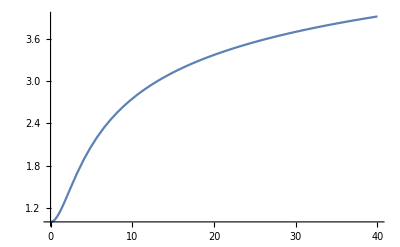

```mathematica
Plot[Evaluate[Sqrt[m1[t]^2+m2[t]^2]/.srl],{t,0,40}]
```

```mathematica
outrl = Table[{t0, (Evaluate[(m1[t]*1/Sqrt[2]+m2[t]*1/Sqrt[2])/Sqrt[m1[t]^2+m2[t]^2]/.srl]/.t->t0)[[1]]},{t0,0.1,40,0.1}];
```

```mathematica
outrl[[All,2]]
```

{0.0499272,0.0994217,0.148069,0.195492,0.241359,0.2854,0.327405,0.367229,0.404782,0.440033,0.47299,0.503703,0.532246,0.558718,0.583228,0.605895,0.626843,0.646193,0.664066,0.680577,0.695835,0.709945,0.723,0.735091,0.746299,0.7567,0.766363,0.775349,0.783717,0.791518,0.7988,0.805606,0.811975,0.817942,0.823539,0.828796,0.83374,0.838394,0.842782,0.846921,0.850832,0.854531,0.858033,0.861352,0.864501,0.867492,0.870335,0.87304,0.875617,0.878073,0.880416,0.882654,0.884793,0.886839,0.888798,0.890674,0.892473,0.894199,0.895856,0.897449,0.898979,0.900452,0.90187,0.903236,0.904553,0.905823,0.907049,0.908232,0.909375,0.91048,0.911549,0.912583,0.913584,0.914554,0.915494,0.916405,0.917288,0.918145,0.918978,0.919786,0.920571,0.921334,0.922077,0.922798,0.923501,0.924184,0.92485,0.925499,0.92613,0.926746,0.927347,0.927933,0.928504,0.929062,0.929606,0.930138,0.930657,0.931165,0.931661,0.932146,0.93262,0.933084,0.933537,0.933981,0.934416,0.934841,0.935258,0.935666,0.936066,0.936458,0.936842,0.937219,0.937588,0.93795,0.938306,0.938654,0.938996,0.939332,0.939662,0.939985,0.940303,0.940615,0.940922,0.941223,0.94152,0.941811,0.942097,0.942378,0.942655,0.942927,0.943195,0.943458,0.943718,0.943973,0.944224,0.944471,0.944714,0.944954,0.94519,0.945422,0.945651,0.945876,0.946098,0.946317,0.946533,0.946746,0.946955,0.947162,0.947366,0.947567,0.947765,0.94796,0.948153,0.948343,0.948531,0.948716,0.948899,0.949079,0.949257,0.949433,0.949606,0.949778,0.949947,0.950114,0.950279,0.950442,0.950603,0.950761,0.950918,0.951074,0.951227,0.951378,0.951528,0.951676,0.951822,0.951967,0.95211,0.952251,0.952391,0.952529,0.952665,0.952801,0.952934,0.953066,0.953197,0.953326,0.953454,0.953581,0.953706,0.95383,0.953953,0.954074,0.954194,0.954313,0.954431,0.954547,0.954662,0.954776,0.954889,0.955001,0.955112,0.955222,0.95533,0.955438,0.955545,0.95565,0.955755,0.955858,0.955961,0.956062,0.956163,0.956263,0.956362,0.95646,0.956557,0.956653,0.956748,0.956843,0.956936,0.957029,0.957121,0.957212,0.957303,0.957392,0.957481,0.957569,0.957657,0.957743,0.957829,0.957914,0.957999,0.958082,0.958165,0.958248,0.958329,0.95841,0.958491,0.958571,0.95865,0.958728,0.958806,0.958883,0.95896,0.959036,0.959111,0.959186,0.95926,0.959334,0.959407,0.95948,0.959552,0.959623,0.959694,0.959765,0.959834,0.959904,0.959973,0.960041,0.960109,0.960176,0.960243,0.96031,0.960376,0.960441,0.960506,0.960571,0.960635,0.960698,0.960762,0.960824,0.960887,0.960949,0.96101,0.961071,0.961132,0.961192,0.961252,0.961311,0.96137,0.961429,0.961487,0.961545,0.961603,0.96166,0.961716,0.961773,0.961829,0.961884,0.96194,0.961995,0.962049,0.962104,0.962157,0.962211,0.962264,0.962317,0.96237,0.962422,0.962474,0.962525,0.962577,0.962628,0.962678,0.962729,0.962779,0.962829,0.962878,0.962927,0.962976,0.963025,0.963073,0.963121,0.963169,0.963216,0.963263,0.96331,0.963357,0.963403,0.96345,0.963495,0.963541,0.963586,0.963631,0.963676,0.963721,0.963765,0.963809,0.963853,0.963897,0.96394,0.963983,0.964026,0.964069,0.964111,0.964153,0.964195,0.964237,0.964279,0.96432,0.964361,0.964402,0.964442,0.964483,0.964523,0.964563,0.964603,0.964643,0.964682,0.964721,0.96476,0.964799,0.964838,0.964876,0.964914,0.964952,0.96499,0.965028,0.965065,0.965102,0.965139,0.965176,0.965213,0.96525,0.965286,0.965322,0.965358,0.965394,0.96543,0.965465,0.9655,0.965536,0.965571,0.965605,0.96564,0.965674,0.965709,0.965743,0.965777,0.965811,0.965844,0.965878,0.965911,0.965945,0.965978,0.966011,0.966043,0.966076,0.966108,0.966141,0.966173,0.966205,0.966237,0.966269,0.9663,0.966332,0.966363,0.966394,0.966425,0.966456,0.966487}

```mathematica
Export["outrlsig1.csv",outrl,"CSV"]
```

outrlsig1.csv

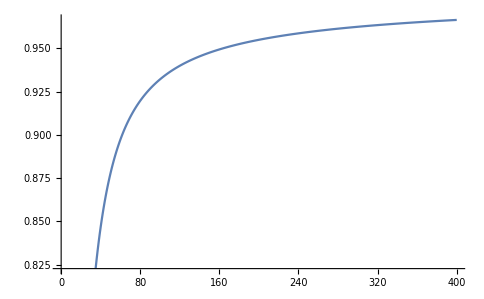

```mathematica
ListLinePlot[{outrl[[All,2]]}]
```

```mathematica
snrrl[sig_]:=(srl = NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],m1'[t]==2*((mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu1*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m1[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sig},
m2'[t]==2*((mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) -mu2*(Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8]]-2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])-sigma/Sqrt[2Pi]*2m2[t] sigma Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2Pi/8] * Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]]*Exp[-1/2*(m1[t] mu1 + m2[t] mu2)^2 *(Pi/8)/(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sig}},{m1,m2},{t,0,40}]; Table[{t0, (Evaluate[(m1[t]*1/Sqrt[2]+m2[t]*1/Sqrt[2])/Sqrt[m1[t]^2+m2[t]^2]/.srl]/.t->t0)[[1]]},{t0,0.1,40,0.005}])
```

```mathematica
longtab = Table[{sig,snrrl[sig]},{sig,0.01,1.01,0.01}]
```

{{0.01,{{0.1,0.0499259},{0.105,0.0524144},{0.11,0.0549018},{0.115,0.0573879},{0.12,0.0598729},{0.125,0.0623565},{0.13,0.0648387},{0.135,0.0673196},{0.14,0.069799},7963,{39.96,0.966502},{39.965,0.966503},{39.97,0.966505},{39.975,0.966506},{39.98,0.966508},{39.985,0.96651},{39.99,0.966511},{39.995,0.966513},{40.,0.966514}}},99,{1.01,1}}
 |  |  |  |

```mathematica
learntimes = Table[{el[[1]],Select[el[[2]], #[[2]]>0.8&,1]},{el,longtab}]
```

{{0.01,{{3.12,0.800199}}},{0.02,{{3.12,0.8002}}},{0.03,{{3.12,0.800203}}},{0.04,{{3.12,0.800206}}},{0.05,{{3.12,0.80021}}},{0.06,{{3.12,0.800215}}},{0.07,{{3.12,0.800221}}},{0.08,{{3.12,0.800227}}},{0.09,{{3.12,0.800234}}},{0.1,{{3.12,0.800241}}},{0.11,{{3.12,0.800248}}},{0.12,{{3.12,0.800254}}},{0.13,{{3.12,0.800261}}},{0.14,{{3.12,0.800266}}},{0.15,{{3.12,0.800271}}},{0.16,{{3.12,0.800275}}},{0.17,{{3.12,0.800278}}},{0.18,{{3.12,0.800279}}},{0.19,{{3.12,0.800278}}},{0.2,{{3.12,0.800275}}},{0.21,{{3.12,0.800269}}},{0.22,{{3.12,0.800261}}},{0.23,{{3.12,0.80025}}},{0.24,{{3.12,0.800236}}},{0.25,{{3.12,0.800218}}},{0.26,{{3.12,0.800196}}},{0.27,{{3.12,0.800171}}},{0.28,{{3.12,0.800141}}},{0.29,{{3.12,0.800106}}},{0.3,{{3.12,0.800067}}},{0.31,{{3.12,0.800022}}},{0.32,{{3.125,0.800341}}},{0.33,{{3.125,0.800287}}},{0.34,{{3.125,0.800227}}},{0.35,{{3.125,0.80016}}},{0.36,{{3.125,0.800088}}},{0.37,{{3.125,0.800009}}},{0.38,{{3.13,0.800298}}},{0.39,{{3.13,0.800207}}},{0.4,{{3.13,0.800109}}},{0.41,{{3.13,0.800003}}},{0.42,{{3.135,0.800269}}},{0.43,{{3.135,0.80015}}},{0.44,{{3.135,0.800023}}},{0.45,{{3.14,0.800271}}},{0.46,{{3.14,0.800129}}},{0.47,{{3.145,0.800364}}},{0.48,{{3.145,0.800208}}},{0.49,{{3.145,0.800043}}},{0.5,{{3.15,0.800257}}},{0.51,{{3.15,0.800077}}},{0.52,{{3.155,0.800277}}},{0.53,{{3.155,0.800081}}},{0.54,{{3.16,0.800267}}},{0.55,{{3.16,0.800055}}},{0.56,{{3.165,0.800227}}},{0.57,{{3.17,0.800392}}},{0.58,{{3.17,0.800155}}},{0.59,{{3.175,0.800306}}},{0.6,{{3.175,0.800053}}},{0.61,{{3.18,0.800188}}},{0.62,{{3.185,0.800316}}},{0.63,{{3.185,0.800039}}},{0.64,{{3.19,0.800153}}},{0.65,{{3.195,0.800259}}},{0.66,{{3.2,0.800358}}},{0.67,{{3.2,0.800049}}},{0.68,{{3.205,0.800133}}},{0.69,{{3.21,0.80021}}},{0.7,{{3.215,0.800279}}},{0.71,{{3.22,0.800342}}},{0.72,{{3.225,0.800397}}},{0.73,{{3.225,0.800041}}},{0.74,{{3.23,0.800082}}},{0.75,{{3.235,0.800116}}},{0.76,{{3.24,0.800142}}},{0.77,{{3.245,0.800162}}},{0.78,{{3.25,0.800175}}},{0.79,{{3.255,0.80018}}},{0.8,{{3.26,0.800179}}},{0.81,{{3.265,0.800171}}},{0.82,{{3.27,0.800157}}},{0.83,{{3.275,0.800135}}},{0.84,{{3.28,0.800107}}},{0.85,{{3.285,0.800072}}},{0.86,{{3.29,0.80003}}},{0.87,{{3.3,0.800392}}},{0.88,{{3.305,0.800338}}},{0.89,{{3.31,0.800277}}},{0.9,{{3.315,0.80021}}},{0.91,{{3.32,0.800136}}},{0.92,{{3.325,0.800056}}},{0.93,{{3.335,0.800381}}},{0.94,{{3.34,0.800289}}},{0.95,{{3.345,0.800191}}},{0.96,{{3.35,0.800087}}},{0.97,{{3.36,0.800388}}},{0.98,{{3.365,0.800272}}},{0.99,{{3.37,0.80015}}},{1.,{{3.375,0.800022}}},{1.01,{{3.385,0.800301}}}}

```mathematica
Table[{el[[1]],el[[2,1,1]]},{el,learntimes}]
```

{{0.01,3.12},{0.02,3.12},{0.03,3.12},{0.04,3.12},{0.05,3.12},{0.06,3.12},{0.07,3.12},{0.08,3.12},{0.09,3.12},{0.1,3.12},{0.11,3.12},{0.12,3.12},{0.13,3.12},{0.14,3.12},{0.15,3.12},{0.16,3.12},{0.17,3.12},{0.18,3.12},{0.19,3.12},{0.2,3.12},{0.21,3.12},{0.22,3.12},{0.23,3.12},{0.24,3.12},{0.25,3.12},{0.26,3.12},{0.27,3.12},{0.28,3.12},{0.29,3.12},{0.3,3.12},{0.31,3.12},{0.32,3.125},{0.33,3.125},{0.34,3.125},{0.35,3.125},{0.36,3.125},{0.37,3.125},{0.38,3.13},{0.39,3.13},{0.4,3.13},{0.41,3.13},{0.42,3.135},{0.43,3.135},{0.44,3.135},{0.45,3.14},{0.46,3.14},{0.47,3.145},{0.48,3.145},{0.49,3.145},{0.5,3.15},{0.51,3.15},{0.52,3.155},{0.53,3.155},{0.54,3.16},{0.55,3.16},{0.56,3.165},{0.57,3.17},{0.58,3.17},{0.59,3.175},{0.6,3.175},{0.61,3.18},{0.62,3.185},{0.63,3.185},{0.64,3.19},{0.65,3.195},{0.66,3.2},{0.67,3.2},{0.68,3.205},{0.69,3.21},{0.7,3.215},{0.71,3.22},{0.72,3.225},{0.73,3.225},{0.74,3.23},{0.75,3.235},{0.76,3.24},{0.77,3.245},{0.78,3.25},{0.79,3.255},{0.8,3.26},{0.81,3.265},{0.82,3.27},{0.83,3.275},{0.84,3.28},{0.85,3.285},{0.86,3.29},{0.87,3.3},{0.88,3.305},{0.89,3.31},{0.9,3.315},{0.91,3.32},{0.92,3.325},{0.93,3.335},{0.94,3.34},{0.95,3.345},{0.96,3.35},{0.97,3.36},{0.98,3.365},{0.99,3.37},{1.,3.375},{1.01,3.385}}

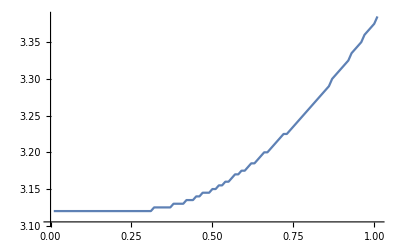

```mathematica
ListLinePlot[Table[{el[[1]],el[[2,1,1]]},{el,learntimes}]]
```

```mathematica
Export["outrllearntimes.csv",Table[{el[[1]],el[[2,1,1]]},{el,learntimes}],"CSV"]
```

outrllearntimes.csv

```mathematica
Table[sigo,Evaluate[Flatten[Select[snrrl[sigo],#[[2]]>0.8&,1]][[1]]],{sigo,0.2,0.1,0.1}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[{m1[0]==1/(√2),m2[0]==-1/(√2),m1'[t]==2 (Power[«2»] Plus[«2»]+1/4 Power[«2»] Power[«2»] m1[«1»] Power[«2»]-1/2 Power[«2»] Power[«2»] Plus[«2»] m1[«1»] Power[«2»]-Power[«2»] Plus[«3»]),m2'[t]==2 (Power[«2»] Plus[«2»]+1/4 Power[«2»] Power[«2»] m2[«1»] Power[«2»]-1/2 Power[«2»] Power[«2»] Plus[«2»] m2[«1»] Power[«2»]-Power[«2»] Plus[«3»])},{m1,m2},{t,0,40}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.1 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{m1[0]==1/(√2),m2[0]==-1/(√2),m1'[0.1]==2 (Power[«2»] Plus[«2»]+1/4 Power[«2»] Power[«2»] m1[«1»] Power[«2»]-1/2 Power[«2»] Power[«2»] Plus[«2»] m1[«1»] Power[«2»]-Power[«2»] Plus[«3»]),m2'[0.1]==2 (Power[«2»] Plus[«2»]+1/4 Power[«2»] Power[«2»] m2[«1»] Power[«2»]-1/2 Power[«2»] Power[«2»] Plus[«2»] m2[«1»] Power[«2»]-Power[«2»] Plus[«3»])},{m1,m2},{0.1,0,40}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{m1[0]==1/(√2),m2[0]==-1/(√2),m1'[t]==2 (Power[«2»] Plus[«2»]+1/4 Power[«2»] Power[«2»] m1[«1»] Power[«2»]-1/2 Power[«2»] Power[«2»] Plus[«2»] m1[«1»] Power[«2»]-Power[«2»] Plus[«3»]),m2'[t]==2 (Power[«2»] Plus[«2»]+1/4 Power[«2»] Power[«2»] m2[«1»] Power[«2»]-1/2 Power[«2»] Power[«2»] Plus[«2»] m2[«1»] Power[«2»]-Power[«2»] Plus[«3»])},{m1,m2},{t,0,40}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.2 cannot be used as a variable.

NDSolve::dsvar: 0.3 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Table::nliter: Non-list iterator {}⟦1⟧ at position 2 does not evaluate to a real numeric value.

Table[sigo,{}⟦1⟧,{sigo,0.2,0.1,0.1}]

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Variance

```mathematica
rlm1rhs[t]=(2*((sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) (1-2Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]])+mu1*(2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])));
rlm2rhs[t]=(2*((sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t] mu1+m2[t] mu2)^2Pi/8)/(1+(m1[t] ^2+m2[t]^2)sigma^2Pi/8)]) (1-2Phi[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[(1+(m1[t]^2 +m2[t]^2)sigma^2 Pi/8)(1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4)]])+mu2*(2OwenT[(m1[t] mu1 +m2[t] mu2)Sqrt[Pi/8]/Sqrt[1+(m1[t]^2+m2[t]^2) sigma^2 Pi/8],1/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/4]])));
```

```mathematica
rlcovterms1[t] =C11[t]D[rlm1rhs[t],m1[t],m1[t]]+
2C12[t]*D[rlm1rhs[t],m1[t],m2[t]]+
C22[t]D[rlm1rhs[t],m2[t],m2[t]];
```

```mathematica
rlcovterms2[t] = C11[t]D[rlm2rhs[t],m1[t],m1[t]]+
2C12[t]*D[rlm2rhs[t],m1[t],m2[t]]+
C22[t]D[rlm2rhs[t],m2[t],m2[t]];
```

```mathematica
rlcovap11[t]=(2*C11[t]*D[rlm1rhs[t],m1[t]]+2*C12[t]*D[rlm1rhs[t],m2[t]])//Simplify;
```

```mathematica
rlcovap12[t]=(C11[t]*D[rlm2rhs[t],m1[t]]+C12[t]*D[rlm1rhs[t],m1[t]]+C12[t]*D[rlm2rhs[t],m2[t]]+C22[t]*D[rlm1rhs[t],m2[t]])//Simplify;
```

```mathematica
rlcovap22[t]=(2*C12[t]*D[rlm2rhs[t],m1[t]]+2*C22[t]*D[rlm2rhs[t],m2[t]])//Simplify;
```

```mathematica
rlsolcovar=Table[NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],C11[0]==0.1,C12[0]==0,C22[0]==0.1,m1'[t]==(rlm1rhs[t]+rlcovterms1[t]-0.1*m1[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},m2'[t]==(rlm2rhs[t]+rlcovterms2[t]-0.1m2[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C11'[t]==(rlcovap11[t]-2C11[t]*0.1)/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C12'[t]==(rlcovap12[t]-2C12[t]*0.1)/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C22'[t]==(rlcovap22[t]-2C22[t]*0.1)/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval}},{m1,m2,C11,C12,C22},{t,0,40}],{sigval,{1,0.5, 0.0}}];
```

```mathematica
Export["outcovtracerlsig10.csv",Table[{tval,(Evaluate[(C11[t]+C22[t])/.rlsolcovar[[1]]]/.t->tval)[[1]]},{tval,0,40,0.1}],"CSV"]
Export["outcovtracerlsig05.csv",Table[{tval,(Evaluate[(C11[t]+C22[t])/.rlsolcovar[[2]]]/.t->tval)[[1]]},{tval,0,40,0.1}],"CSV"]
Export["outcovtracerlsig00.csv",Table[{tval,(Evaluate[(C11[t]+C22[t])/.rlsolcovar[[3]]]/.t->tval)[[1]]},{tval,0,40,0.1}],"CSV"]
```

outcovtracerlsig10.csv

outcovtracerlsig05.csv

outcovtracerlsig00.csv

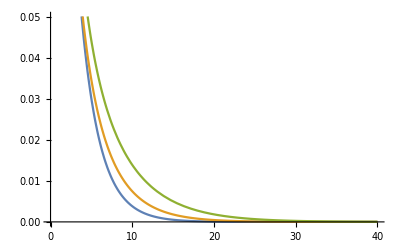

```mathematica
Plot[{Evaluate[(C11[t]+C22[t])/.rlsolcovar[[1]]],Evaluate[(C11[t]+C22[t])/.rlsolcovar[[2]]],Evaluate[(C11[t]+C22[t])/.rlsolcovar[[3]]]},{t,0,40}]
```